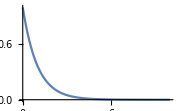

```mathematica
Plot[Exp[-x],{x,0.000,10^1},PlotRange->Full]
```

```mathematica
f[x_]:=1-Exp[-x]
```

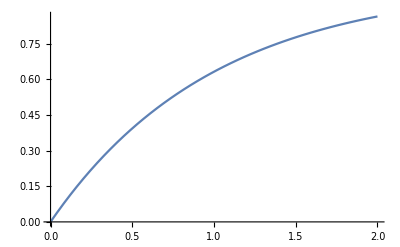

```mathematica
Plot[f[x],{x,0.0,2},PlotRange->Full]
```

```mathematica
f[4]//N
f[2]//N
f[1]//N
f[0.7]//N
f[0.07]//N
```

0.981684

0.864665

0.632121

0.503415

0.0676062

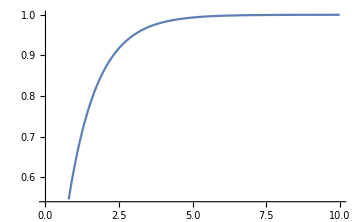
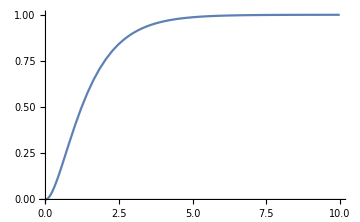

```mathematica
{Plot[f[y]           ,{y,0,10},ImageSize->Medium],
Plot[f[y] f[y],{y,0,10},ImageSize->Medium]}
```

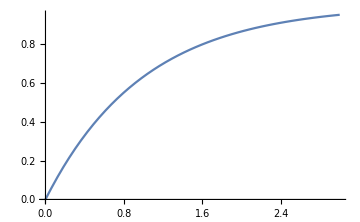
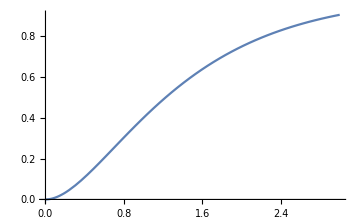

```mathematica
{Plot[f[y]           ,{y,0,3},ImageSize->Medium],
Plot[f[y] f[y],{y,0,3},ImageSize->Medium]}
```